# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="ee-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",GenericModel->"Lorentz",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

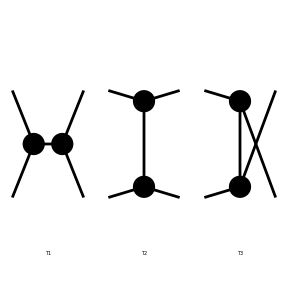

```mathematica
topsBorn=CreateTopologies[0,2->2,Adjacencies->3];
Paint[topsBorn];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 3: 0 Generic, 0 Classes, 0 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

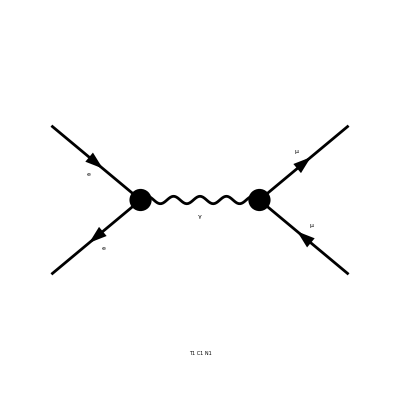

```mathematica
insBorn=InsertFields[topsBorn, process,QEDOnly];
Paint[insBorn];
```

## Feynman Amplitudes

```mathematica
ClearProcess[]
```

```mathematica
ampBorn=CalcFeynAmp[CreateFeynAmp[insBorn,AmplitudeLevel->{Particles}],FermionChains -> VA]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

preparing FORM code in /home/riccardo/fc-amp-8.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F5]]

## Squared Matrix Element

```mathematica
_Hel=0;
```

```mathematica
smBorn=SquaredME[ampBorn]//Simplify;
smBorn=smBorn/.HelicityME[smBorn];
smBorn=PolarizationSum[smBorn]//Simplify
```

> 1 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-8.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-8.frm

running FORM...

ok

8 Alfa2 π^2 (4 ME2 MM2+T^2+2 (ME2^2+MM2^2+(ME2+MM2) (S-T-U))+U^2) Den[S,0]^2

## One-Loop

## Topologies

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 3 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 4 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 5 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 6 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 7 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 8 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 9 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 10 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 11 aebf/cfde/egfhghgh.m, 0 diagrams

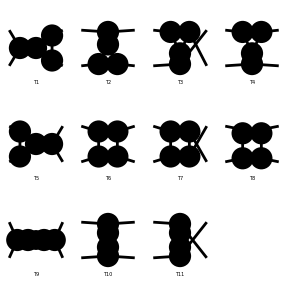

```mathematica
tops1=CreateTopologies[1,2->2,Adjacencies->3,ExcludeTopologies->{Tadpoles,WFCorrections}];
tops1=Delete[tops1,4];
Paint[tops1];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 3: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 4: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 5: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 6: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 7: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 8: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 9: 1 Generic, 3 Classes, 9 Particles insertions

> Top. 10: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 11: 0 Generic, 0 Classes, 0 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 5 Generic, 7 Classes, 13 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 5 aebe/cfdf/egfhghgh.m, 0 diagrams

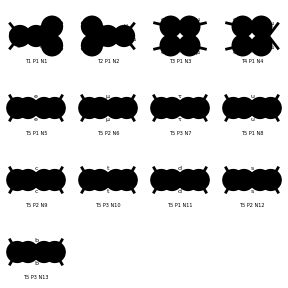

```mathematica
ins1=InsertFields[tops1, process,QEDOnly];
Paint[ins1, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
amp1Loop=CalcFeynAmp[CreateFeynAmp[ins1,AmplitudeLevel->{Particles}],FermionChains->Chiral];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/riccardo/fc-amp-8.frm

running FORM...

ok

## FormCalc results

```mathematica
sm1Loop=SquaredME[ampBorn,amp1Loop]//HelicityME//PolarizationSum
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-8.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-8.frm

running FORM...

ok

0

```mathematica
UVDivergentPart[result1]/.Subexpr[]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa EL (F1+F2) (Divergence+12 Divergence MM2 Den[MM2,MM2]))/(4 π)]

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]
```

## Computations

```mathematica
Length[amp1]
```

3

```mathematica
result1List=calcFeynAmpList[amp1]/.result1List[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]//Simplify
```

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2))/(4 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)]]

```mathematica
uvDivL=Map[#[[1]]&,uvDiv]/.uvDivL[[0]]->List
```

{-(Alfa Divergence EL (F1+F2))/(4 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)}